# Tabbed UpSet Chart

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<UpSetChart`
```

## Load Data

```mathematica
dd=UpSetChart`TestData`DummyData[3]
```

<|Red→{Strawberry,Apple},Green→{Kiwi,Pear,Cucumber,Pickle},Tasty→{Kiwi,Pear},Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Vegetable→{Cucumber,Pickle}|>

## Do calculations

```mathematica
calc=UpSetChart`Calculations`CalcThenSortAndFilter[dd]
```

<|sets→<|Fruit→{Kiwi,Lemon,Banana,Strawberry,Pear,Apple,Carrot},Green→{Kiwi,Pear,Cucumber,Pickle},Red→{Strawberry,Apple},Tasty→{Kiwi,Pear},Vegetable→{Cucumber,Pickle}|>,comparisons→<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
gb=GroupBy[calc["comparisons"],Length[#]&]
```

<|3→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
GroupBy[calc["comparisons"],Length[#]&]
```

<|3→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

```mathematica
Key@calc["comparisons"]
```

Key[<|{Fruit}→{Banana,Carrot,Lemon},{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry},{Green,Tasty,Fruit}→{Kiwi,Pear}|>]

```mathematica
gb=Map[Association@@Map[#-> calc["comparisons"][#]&,#]&,
GroupBy[Keys@calc["comparisons"],Length@#&]]
```

<|1→<|{Fruit}→{Banana,Carrot,Lemon}|>,2→<|{Green,Vegetable}→{Cucumber,Pickle},{Red,Fruit}→{Apple,Strawberry}|>,3→<|{Green,Tasty,Fruit}→{Kiwi,Pear}|>|>

## Calculate components by size

```mathematica
gc=UpSetChart`Graphics`Utilities`GraphicComponents;
```

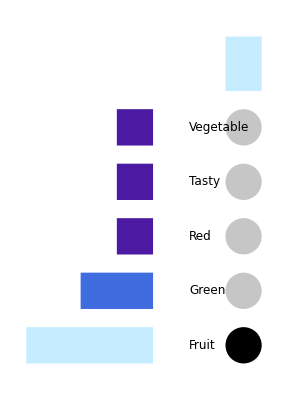
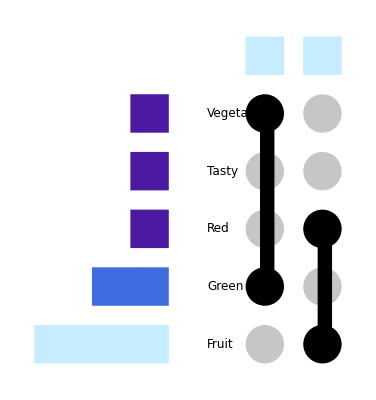
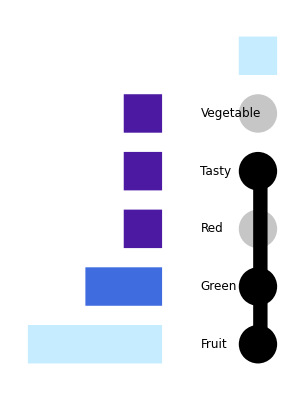
<|1→-Graphics-,2→-Graphics-,3→-Graphics-|>

```mathematica
(*gbgc=Graphics[#,ImageSize->{400,100}
(*, BaselinePosition->Bottom*)
(*, AlignmentPoint->{0,0}*)
]&/@(gc[calc["sets"],# ]&/@gb)*)
gbgc=Graphics[#
(*, BaselinePosition->Bottom*)
(*, AlignmentPoint->{0,0}*)
]&/@(gc[calc["sets"],#]&/@gb)
```

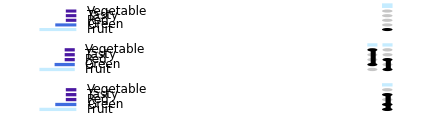

```mathematica
GraphicsColumn[Values[gbgc]]
```

```mathematica
TabView[KeySortBy[gbgc,#&],
Alignment->{Left,Bottom},
ContentPadding->False,
AutoAction->True,
BaselinePosition->Bottom,
ControlPlacement->Left,
ImageMargins->0,
FrameMargins-> 0,
ImageSize->{Automatic,1}
]
```

123

```mathematica
Manipulate[
"Hello"
,
Dynamic@Table[{{ToString@set, True, ToString@set},{True, False}, Checkbox},{set,Keys@calc["sets"]}],
ControlPlacement->Left

]
```

{Checkbox[{Fruit,{True,False}}],Checkbox[{Green,{True,False}}],Checkbox[{Red,{True,False}}],Checkbox[{Tasty,{True,False}}],Checkbox[{Vegetable,{True,False}}]}

```mathematica
DynamicModule[
{n=5,data=Table[RandomReal[],20],checks=Table[False,{Length[calc["sets"]]}]},
Column[{Slider[Dynamic[n],{1,5,1}],
Dynamic@Table[Row[{ToString[(Keys@calc["sets"])[[k]]]<>" = ",With[{k=k},Checkbox[Dynamic[checks[[k]]],{True,False}]]}],{k,n}],
Dynamic[Keys@calc["sets"]],
Dynamic[checks]
}]
]
```

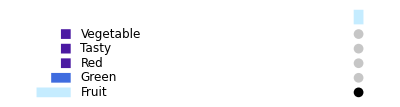
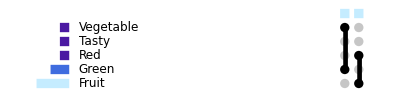
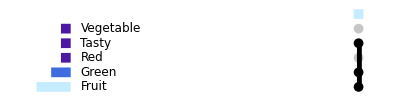
<|1→-Graphics-,2→-Graphics-,3→-Graphics-|>

```mathematica
gbgc
```

```mathematica
Table[{{ToString@set, True, ToString@set},{True, False}, Checkbox},{set,Keys@calc["sets"]}]
```

{{{Fruit,True,Fruit},{True,False},Checkbox},{{Green,True,Green},{True,False},Checkbox},{{Red,True,Red},{True,False},Checkbox},{{Tasty,True,Tasty},{True,False},Checkbox},{{Vegetable,True,Vegetable},{True,False},Checkbox}}

{Fruit,Green,Red,Tasty,Vegetable}

```mathematica
sets = calc["sets"];

DynamicModule[
{
checks=Table[True,{Length[sets]}],
keys=Keys[sets],
numSets=Length[sets]
},
Column[
{

Dynamic[
Labeled[
Row[
Table[
Row[
{
ToString[keys[[k]]]<>": ",
With[{k=k},Checkbox[Dynamic[checks[[k]]],{False,True}]],
If[k≠numSets,",\t",""]
}
],{k,numSets}]
],"Use sets: ", Left]
],

Dynamic[
With[
{filt=Table[If[checks[[k]],keys[[k]], Nothing],{k, numSets}]},
UpSetChart[Association@@FilterRules[sets,filt]]
]
]
}
]
]
```